```mathematica
Integrate[E^(-ω^2+ⅈ*ω*x), {ω, -∞, ∞}]
```

ⅇ^(-x^2/4) √π

(√2 ⅇ^(x^2/(4 (-1+t))))/(√(2-2 t))

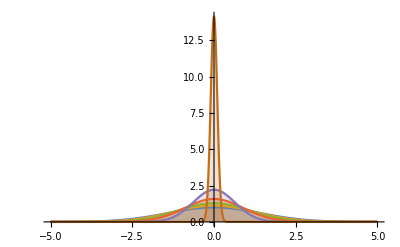

```mathematica
heqn=D[u[x,t],t]==-D[u[x,t],{x,2}];
ic=u[x,0]==E^(-x^2/4);
sol=DSolveValue[{heqn,ic},u[x,t],{x,t}]
Plot[Evaluate[Table[sol,{t,0,1, .2 - .001}]],{x,-5,5},PlotRange->All,Filling->Axis]
```

{0.001,0.111,0.221,0.331,0.441,0.551,0.661,0.771,0.881,0.991}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

{1.59577,1.60208,1.62138,1.65566,1.70898,1.78918,1.91271,2.12091,2.57147,7.57356}

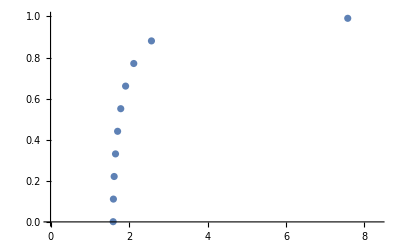

```mathematica
Clear[F]
F[K_?NumericQ, r_] := NIntegrate[g[K*r*Sin[θ]]*Cos[θ]^2*K, {θ, -π/2, π/2}]
g[x_] := E^(-x^2/2)/Sqrt[2π]

rs = Table[r, {r, .001, .999, .11}]
Ks = Table[
K /. NSolve[F[K, r] == 1, K][[1]],
{r, rs}]
ListPlot[Transpose[{Ks, rs}], PlotRange->{{0, Max[Ks]*1.1}, {0, 1}}]
```

0.920344

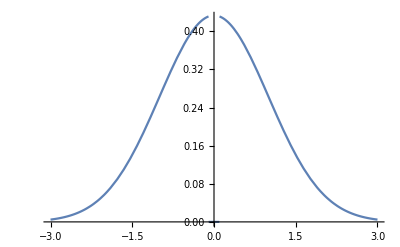

{0.02,0.05,0.08,0.11,0.14,0.17,0.2,0.23,0.26,0.29,0.32,0.35,0.38,0.41,0.44,0.47,0.5,0.53,0.56,0.59,0.62,0.65,0.68,0.71,0.74,0.77,0.8,0.83,0.86,0.89,0.92,0.95,0.98}

10.3656  2.86667

10.3656  2.86667

10.3656  2.86667

7.42641  1.06857

7.42641  1.06857

7.42641  1.06857

7.30638  1.00034

7.30638  1.00034

7.30638  1.00034

7.30577  1.

7.30577  1.

7.30577  1.

«3 more identical outputs»

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

4.36563  1.28646

4.36563  1.28646

4.36563  1.28646

3.91745  1.00198

3.91745  1.00198

3.91745  1.00198

3.9143  1.

3.9143  1.

3.9143  1.

«6 more identical outputs»

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

2.86563  0.891894

2.86563  0.891894

2.86563  0.891894

3.03397  1.00023

3.03397  1.00023

3.03397  1.00023

3.03361  1.

3.03361  1.

3.03361  1.

«3 more identical outputs»

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

2.18381  0.712801

2.18381  0.712801

2.18381  0.712801

2.62952  1.00103

2.62952  1.00103

2.62952  1.00103

2.62794  1.

2.62794  1.

2.62794  1.

«3 more identical outputs»

1.7942  0.610605

1.7942  0.610605

1.7942  0.610605

2.3971  1.00056

2.3971  1.00056

2.3971  1.00056

2.39623  1.

2.39623  1.

2.39623  1.

«3 more identical outputs»

1.5421  0.544558

1.5421  0.544558

1.5421  0.544558

2.24619  0.9988

2.24619  0.9988

2.24619  0.9988

2.24807  1.

2.24807  1.

2.24807  1.

«5 more identical outputs»

1.36563  0.498367

1.36563  0.498367

1.36563  0.498367

2.14049  0.996021

2.14049  0.996021

2.14049  0.996021

2.14678  0.999999

2.14678  0.999999

2.14678  0.999999

2.14678  1.

2.14678  1.

2.14678  1.

«3 more identical outputs»

1.23519  0.464242

1.23519  0.464242

1.23519  0.464242

2.06254  0.992448

2.06254  0.992448

2.06254  0.992448

2.07465  0.999997

2.07465  0.999997

2.07465  0.999997

2.07466  1.

2.07466  1.

2.07466  1.

«3 more identical outputs»

1.13486  0.437993

1.13486  0.437993

1.13486  0.437993

2.00291  0.988234

2.00291  0.988234

2.00291  0.988234

2.02209  0.999989

2.02209  0.999989

2.02209  0.999989

2.02211  1.

2.02211  1.

2.02211  1.

«3 more identical outputs»

1.05528  0.417165

1.05528  0.417165

1.05528  0.417165

1.95604  0.983476

1.95604  0.983476

1.95604  0.983476

1.98347  0.999973

1.98347  0.999973

1.98347  0.999973

1.98352  1.

1.98352  1.

1.98352  1.

«3 more identical outputs»

0.990626  0.400225

0.990626  0.400225

0.990626  0.400225

1.91845  0.978241

1.91845  0.978241

1.91845  0.978241

1.95529  0.999943

1.95529  0.999943

1.95529  0.999943

1.95539  1.

1.95539  1.

1.95539  1.

«3 more identical outputs»

0.937055  0.386167

0.937055  0.386167

0.937055  0.386167

1.88781  0.972573

1.88781  0.972573

1.88781  0.972573

1.93526  0.99989

1.93526  0.99989

1.93526  0.99989

1.93546  1.

1.93546  1.

1.93546  1.

«3 more identical outputs»

0.891942  0.374302

0.891942  0.374302

0.891942  0.374302

1.86254  0.966505

1.86254  0.966505

1.86254  0.966505

1.92187  0.999805

1.92187  0.999805

1.92187  0.999805

1.92222  1.

1.92222  1.

1.92222  1.

«3 more identical outputs»

0.853431  0.364146

0.853431  0.364146

0.853431  0.364146

1.84152  0.96006

1.84152  0.96006

1.84152  0.96006

1.91406  0.999672

1.91406  0.999672

1.91406  0.999672

1.91467  1.

1.91467  1.

1.91467  1.

«5 more identical outputs»

0.820171  0.355345

0.820171  0.355345

0.820171  0.355345

1.82392  0.953259

1.82392  0.953259

1.82392  0.953259

1.91112  0.999474

1.91112  0.999474

1.91112  0.999474

1.91212  1.

1.91212  1.

1.91212  1.

«5 more identical outputs»

0.791158  0.347636

0.791158  0.347636

0.791158  0.347636

1.80912  0.946118

1.80912  0.946118

1.80912  0.946118

1.91255  0.999188

1.91255  0.999188

1.91255  0.999188

1.91416  1.

1.91416  1.

1.91416  1.

«6 more identical outputs»

0.765626  0.34082

0.765626  0.34082

0.765626  0.34082

1.79664  0.938653

1.79664  0.938653

1.79664  0.938653

1.91804  0.998785

1.91804  0.998785

1.91804  0.998785

1.92054  0.999999

1.92054  0.999999

1.92054  0.999999

1.92054  1.

1.92054  1.

1.92054  1.

«3 more identical outputs»

0.742984  0.334744

0.742984  0.334744

0.742985  0.334744

1.78613  0.930878

1.78613  0.930878

1.78613  0.930878

1.92738  0.998228

1.92738  0.998228

1.92738  0.998229

1.93119  0.999999

1.93119  0.999999

1.93119  0.999999

1.93119  1.

1.93119  1.

1.93119  1.

«3 more identical outputs»

0.722769  0.329286

0.722769  0.329286

0.722769  0.329286

1.7773  0.922807

1.7773  0.922807

1.7773  0.922807

1.94047  0.997475

1.94047  0.997475

1.94047  0.997475

1.94618  0.999997

1.94618  0.999997

1.94618  0.999997

1.94618  1.

1.94618  1.

1.94618  1.

«3 more identical outputs»

0.704609  0.32435

0.704609  0.32435

0.704609  0.324351

1.76991  0.914456

1.76991  0.914456

1.76991  0.914456

1.95729  0.996473

1.95729  0.996473

1.95729  0.996473

1.96571  0.999993

1.96571  0.999993

1.96571  0.999993

1.96573  1.

1.96573  1.

1.96573  1.

«3 more identical outputs»

0.688207  0.31986

0.688207  0.31986

0.688207  0.31986

1.76378  0.905839

1.76378  0.905839

1.76378  0.905839

1.9779  0.995158

1.9779  0.995158

1.9779  0.995158

1.99017  0.999984

1.99017  0.999984

1.99017  0.999984

1.99021  1.

1.99021  1.

1.99021  1.

«3 more identical outputs»

0.673318  0.315752

0.673318  0.315752

0.673318  0.315752

1.75875  0.896972

1.75875  0.896972

1.75875  0.896972

2.00242  0.993459

2.00242  0.993459

2.00242  0.993459

2.02013  0.999966

2.02013  0.999966

2.02013  0.999966

2.02022  1.

2.02022  1.

2.02023  1.

2.02022  1.

2.02022  1.

2.02022  1.

0.659744  0.311974

0.659744  0.311974

0.659744  0.311974

1.7547  0.887869

1.7547  0.887869

1.7547  0.887869

2.03102  0.99129

2.03102  0.99129

2.03102  0.99129

2.0564  0.999929

2.0564  0.999929

2.0564  0.999929

2.05661  1.

2.05661  1.

2.05661  1.

«3 more identical outputs»

0.647316  0.308483

0.647316  0.308483

0.647316  0.308483

1.75153  0.878548

1.75153  0.878548

1.75153  0.878548

2.06394  0.988558

2.06394  0.988558

2.06394  0.988558

2.1001  0.999856

2.1001  0.999856

2.1001  0.999856

2.10057  1.

2.10057  1.

2.10057  1.

«5 more identical outputs»

0.635896  0.305244

0.635896  0.305244

0.635896  0.305244

1.74915  0.869025

1.74915  0.869025

1.74915  0.869025

2.10147  0.985157

2.10147  0.985157

2.10147  0.985157

2.15283  0.999711

2.15283  0.999711

2.15283  0.999711

2.15386  1.

2.15386  1.

2.15386  1.

«6 more identical outputs»

0.625366  0.302226

0.625366  0.302226

0.625366  0.302226

1.74748  0.859317

1.74748  0.859317

1.74748  0.859317

2.14396  0.980976

2.14396  0.980976

2.14396  0.980976

2.21677  0.999434

2.21677  0.999434

2.21677  0.999434

2.21907  0.999999

2.21907  0.999999

2.21907  0.999999

2.21907  1.

2.21907  1.

2.21907  1.

«3 more identical outputs»

0.615626  0.299402

0.615626  0.299402

0.615626  0.299402

1.74646  0.849441

1.74646  0.849441

1.74646  0.849441

2.19182  0.975899

2.19182  0.975899

2.19182  0.975899

2.29504  0.998914

2.29504  0.998914

2.29504  0.998914

2.30015  0.999997

2.30015  0.999997

2.30015  0.999997

2.30016  1.

2.30016  1.

2.30016  1.

«3 more identical outputs»

0.60659  0.296753

0.60659  0.296753

0.60659  0.296753

1.74604  0.839414

1.74604  0.839414

1.74604  0.839414

2.24555  0.969813

2.24555  0.969813

2.24555  0.969813

2.39209  0.997955

2.39209  0.997955

2.39209  0.997955

2.40354  0.999988

2.40354  0.999988

2.40354  0.999988

2.4036  1.

2.4036  1.

2.4036  1.

«3 more identical outputs»

0.598184  0.294257

0.598184  0.294257

0.598184  0.294257

1.74617  0.829255

1.74617  0.829255

1.74617  0.829255

2.30568  0.962614

2.30568  0.962614

2.30568  0.962614

2.51438  0.99624

2.51438  0.99624

2.51438  0.99624

2.54045  0.999949

2.54045  0.999949

2.54045  0.999949

2.54082  1.

2.54082  1.

2.54082  1.

«5 more identical outputs»

0.590345  0.2919

0.590345  0.2919

0.590345  0.2919

1.74681  0.818982

1.74681  0.818982

1.74681  0.818982

2.37287  0.954217

2.37287  0.954217

2.37287  0.954217

2.67137  0.993273

2.67137  0.993273

2.67137  0.993273

2.73225  0.999778

2.73225  0.999778

2.73225  0.999778

2.7344  1.

2.7344  1.

2.7344  1.

«6 more identical outputs»

0.583017  0.289667

0.583017  0.289667

0.583017  0.289667

1.74793  0.808612

1.74793  0.808612

1.74793  0.808612

2.44781  0.944568

2.44781  0.944568

2.44781  0.944568

2.87711  0.98838

2.87711  0.98838

2.87711  0.98838

3.02399  0.999092

3.02399  0.999092

3.02399  0.999092

3.03752  0.999993

3.03752  0.999993

3.03752  0.999993

3.03763  1.

3.03763  1.

3.03763  1.

«3 more identical outputs»

0.576152  0.287545

0.576152  0.287545

0.576152  0.287545

1.7495  0.798164

1.7495  0.798164

1.7495  0.798164

2.53133  0.933656

2.53133  0.933656

2.53133  0.933656

3.15251  0.980822

3.15251  0.980822

3.15251  0.980822

3.51997  0.996695

3.51997  0.996695

3.51997  0.996695

3.61296  0.999854

3.61296  0.999854

3.61296  0.999854

3.61747  1.

3.61747  1.

3.61747  1.

3.61748  1.

3.61748  1.

3.61748  1.

«3 more identical outputs»

0.569708  0.285524

0.569708  0.285524

0.569708  0.285524

1.75149  0.787654

1.75149  0.787654

1.75149  0.787654

2.62434  0.921517

2.62434  0.921517

2.62434  0.921517

3.52868  0.970089

3.52868  0.970089

3.52868  0.970089

4.47457  0.99026

4.47457  0.99026

4.47457  0.99026

5.16048  0.998026

5.16048  0.998026

5.16048  0.998026

5.38006  0.999875

5.38006  0.999875

5.38006  0.999875

5.39593  0.999999

5.39593  0.999999

5.39593  0.999999

5.39601  1.

5.39601  1.

5.39601  1.

«3 more identical outputs»

{7.30577,3.9143,3.03361,2.62794,2.39623,2.24807,2.14678,2.07466,2.02211,1.98352,1.95539,1.93546,1.92222,1.91467,1.91212,1.91416,1.92054,1.93119,1.94618,1.96573,1.99021,2.02022,2.05661,2.10057,2.15386,2.21907,2.30016,2.4036,2.54082,2.7344,3.03763,3.61748,5.39601}

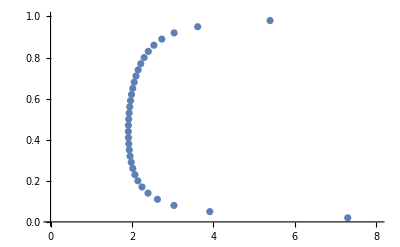

```mathematica
Clear[F]
F[K_?NumericQ, A_, r_] := (L = K + A; Print[L, "  ", NIntegrate[g[L*r*Sin[θ]]*Cos[θ]^2*L, {θ, -π/2, π/2}]];
NIntegrate[g[L*r*Sin[θ]]*Cos[θ]^2*L, {θ, -π/2, π/2}])

w = .1;
g[x_] := Piecewise[{{E^(-x^2/2)/Sqrt[2π], Abs[x] > w}}, 0]
norm = NIntegrate[g[x], {x, -∞, ∞}]
g[x_] := Piecewise[{{E^(-x^2/2)/Sqrt[2π], Abs[x] > w}}, 0]/norm
Plot[g[x], {x, -3, 3}]

rs = Table[r, {r, .02, .999, .03}]
Ks = Table[
(K /. NSolve[F[K, 2*w/r, r] == 1, K][[1]]) + 2*w/r,
{r, rs}]
ListPlot[Transpose[{Ks, rs}], PlotRange->{{0, Max[Ks]*1.1}, {0, 1}}]
```

```mathematica
F[3, 0, .95]
```

3  0.97215

0.97215

```mathematica
1/(a + b*ⅈ) // FullSimplify
```

1/(a+ⅈ b)